## Number Density Rotation Angle Simulation

{0.1×10^12,0.3×10^12,1×10^12,3×10^12,4.9×10^12,10×10^12,30×10^12,100×10^12}

Range

ImplicitRegion[(δ≥-30&&δ≤-10)||(δ≤30&&δ≥10),{δ}]

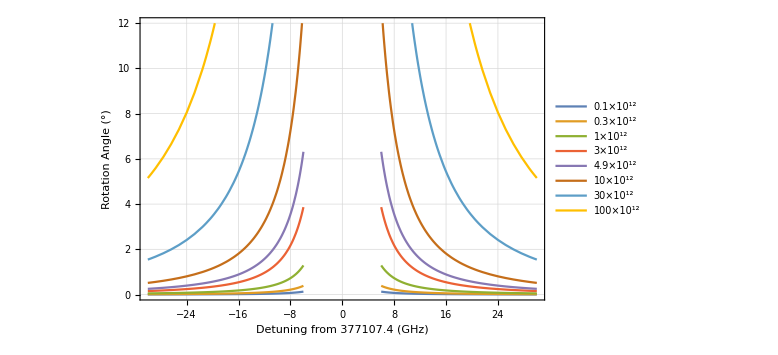

```mathematica
SetDirectory[$PACKAGES];
Import["faradayRotation.wl"];
ResetDirectory[];
(* Enter number density *)
nRb={.1*^12,.3*^12,1*^12,3*^12,4.9*^12,10*^12,30*^12,100*^12};  
nRbLabels=Map[StringJoin[ToString[#],"×10^12"]&,{.1,.3,1,3,4.9,10,30,100}]
Range
(* converts number density and magnetic field into the fitting parameter used in our fit equation.*)
a2[nRb_,BdotL_:300]:=BdotL*nRb/nDensC;
(* 
Define a region over which to plot the function.
This allows for a more flexible region specification
over multiple ranges. The advantage of doing this is that the
function won't be plotted over the small detuning range where we 
never measure the angle and it is very large.
*)
region=ImplicitRegion[(δ≥-30&&δ≤ -10) || (δ≤ 30&&δ≥ 10),{δ}]
xLabel="Detuning from 377107.4 (GHz)";
yLabel="Rotation Angle (°)";
functions=faradayRotationDensityModel[δ,a2[nRb]]*180/π;
Plot[functions,{δ} ∈ Interval[{-30,-6},{6,30}],PlotRange->{0,12},ImageSize->Large,FrameLabel->{xLabel,yLabel},PlotLegends->nRbLabels]
```

```mathematica
-
```

```mathematica
faradayRotationDensityModel[δ,a2[nRb]]
```

{(5.69213×10^-12 (377107.+δ)^2)/δ^2,(2.84606×10^-11 (377107.+δ)^2)/δ^2}

```mathematica
Log10[10]
```

1